```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/lederstrumpf/Development_Dirty_Playground/Casper/p2pvoting/visualization

## Clique Signalling Circle

```mathematica
SelectLargestGroup[cliques_,id_]:=Select[cliques,MemberQ[#,ToString@id]&]
Clear@CircleInCliqueCheap;
CircleInCliqueCheap[frame_,totalFrames_,cliques_,viewingValidator_,supercliques_,{xc_,yc_},radius_]:=Module[{validator=xc},
If[frame==totalFrames
∧Intersection[supercliques,cliques]≠{}
∧MemberQ[MaximalBy[cliques,Length]//First,validator]
(*∧viewingValidator == validator*),
{Red,Disk[{xc,yc},radius]},
If[viewingValidator==validator+1,
{Green,Disk[{xc,yc},radius]},
{Gray,Disk[{xc,yc},radius]}]
(*{Gray,Disk[{xc,yc},radius]}*)
]
]
```

## Circle Function

```mathematica
Clear[CircleFnCheap]
Clear[CircleCurriedCheap]
CircleFnCheap[frame_,totalFrames_,cliques_,viewingValidator_,supercliques_,{xc_,yc_},name_,{w_,h_}]:=Module[{},
CircleInCliqueCheap[frame,totalFrames,cliques,viewingValidator,supercliques,{IntegerPart@xc,yc},0.2]
]
CircleCurriedCheap[frame_,totalFrames_,cliques_,viewingValidator_,supercliques_]:=Function[{a,b,c}, CircleFnCheap[frame,totalFrames,cliques,viewingValidator,supercliques,a,b,c]]
```

## Arrowhead

```mathematica
ScalingFactor=4;
ℛ=Triangle[{{0,-ScalingFactor},{0,ScalingFactor},{-ScalingFactor,0}}];
Hed=Graphics[{Red,ℛ}];
ef[pts_List,e_]:=
Block[{s=0.015,g=Hed},{Arrowheads[{{s,0.5,g}}],Arrow[pts]}]
```

## Data Processing Some Receivers

```mathematica
PlayData=Import["processedxx"<>StringPadLeft[ToString@#,2,"0"]<>".json","RawJSON"]&/@Range[0,99];
```

```mathematica
Drt=With[{viewingValidator=2,index=22},
Table[
validatorSequences=(Values@Values@PlayData[[index,j]]["lms"][[viewingValidator,1]])[[All,1,;;-2,1]];(*Note: This is just cheap hack to have validator profess longest chain they see*)
MaximalBy[validatorSequences,Length],
{j,Length@PlayData[[index]]}]]
```

{{{0}},{{1,0}},{{1,0}},{{1,0}},{{1,1,0}},{{1,1,0}},{{1,1,0}},{{1,1,1,0}},{{1,1,1,0}}}

```mathematica
Final[file_,viewingValidator_]:=
Module[{},
Data=file;
Drt=
Table[
validatorSequences=(Values@Values@file[[j]]["lms"][[viewingValidator,1]])[[All,1,;;-2,1]];
(*Note: This is just cheap hack to have validator profess longest chain they see*)
MaximalBy[validatorSequences,Length]//First//Reverse,
{j,Length@Data}];

SuperCliques=MaximalBy[Join@@file[[-1]]["clqs"],Length]//DeleteDuplicates;

Table[Module[{index=i},
Dyt={ToExpression@Drt[[index,#]],#}&/@Range@Length@Drt[[index]];
Dut=Dyt[[#,2]]->Dyt[[#+1,2]]&/@Range[Length[Dyt]-1];
DitFinal=Drt[[-1]];
DytFinal={ToExpression@DitFinal[[#]],#}&/@Range@Length@DitFinal;
DutFinal=DytFinal[[#,2]]->DytFinal[[#+1,2]]&/@Range[-1+Length@DytFinal];
Show[
Graph[
DutFinal,
VertexCoordinates->DytFinal,
EdgeShapeFunction->GraphElementData["CarvedArrow","ArrowSize"->Medium],
VertexStyle->White,
EdgeStyle->White,
BaseStyle->EdgeForm[None],
GraphHighlightStyle->"DehighlightHide",
ImageSize->Small],

Graphics[Text[Style["View "<>ToString@viewingValidator,Large],{1.0,0}]],
Graph[
Dut,
VertexCoordinates->Dyt,
EdgeShapeFunction->ef,
(*VertexLabels->Automatic,*)
(*VertexStyle->Red,*)
VertexShapeFunction-> CircleCurriedCheap[i,Length@Drt,file[[i]]["clqs"][[viewingValidator]],viewingValidator,SuperCliques],
VertexSize->0.25,
EdgeStyle->Thickness@0.03]
(*If[i==Length@Drt,Graphics[{Blue,Disk[{0,1},0.25]}],Graphics[]]*)
]
(*,Data[[i]]["clqs"][[1]]*)],{i,Length@Drt}]]
```

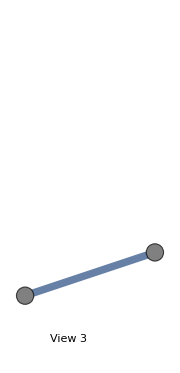
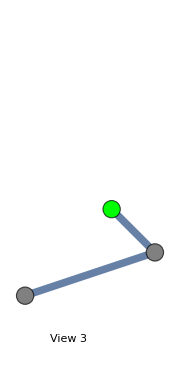
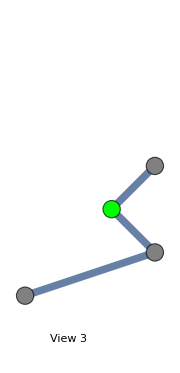
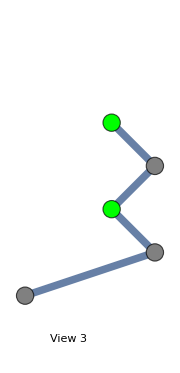
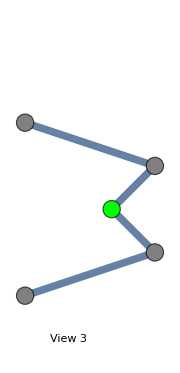
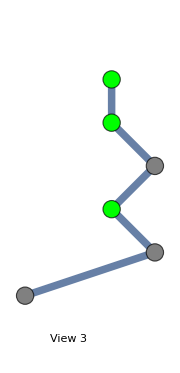
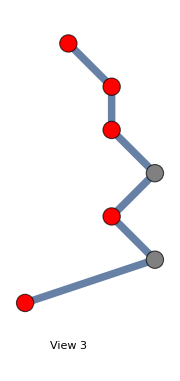
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Final[PlayData[[21]],3]
```

```mathematica
Manipulate[ListAnimate[Transpose[Final[PlayData[[index]],#][[1;;-1]]&/@Range@ToExpression@PlayData[[index]][[1]]["sendercount"]]],{index,1,99,1}]
```